## Иваненко И.Л.

## Лабораторная работа №5 ПО-4

## 5.1

#### 5.1.а | Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

#### 5.1.б | Введение дополнительных пробелов не изменяют результата вычислений

```mathematica
3   5
```

15

```mathematica
2+         7
```

9

#### 5.1.в | Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя

```mathematica
2/3
```

2/3

```mathematica
17^(1/2)
```

√17

#### 5.1.г | Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды

```mathematica
3 /7.
```

0.428571

```mathematica
17.^(1/2)
```

4.12311

#### 5.1.д | Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
5     (4-1)
```

15

## 5.2

#### 5.2.а | С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17],200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

#### 5.2.б | Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[E^(Pi*Sqrt[163]),40]] - N[E^(Pi*Sqrt[163]), 40] (* FIX *)
Round[N[E^(Pi*Sqrt[163]),40]]
N[E^(Pi*Sqrt[163]), 40]
```

7.499274028×10^-13

262537412640768744

2.625374126407687439999999999992500725972×10^17

#### 5.2.в | Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

#### 5.2.г | Последовательно введите выражения | Справедливо ли неравенство

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## 5.3

#### 5.3.а | Решить уравнения

```mathematica
NSolve[Sqrt[x+2]+4*x==4,x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

#### 5.3.б | Решить системы уравнений

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

#### 5.3.в | Придумать уравнение или систему уравнений и найдите её численное решение

```mathematica
NSolve[{x^3+y^3+3*x^2*y+3*y^2*x==64,x+3*y==8}, {x,y},Reals]
```

{{x→2.,y→2.}}

## 5.4

#### Вариант 10 | x^2 + E^-x - 2 == Sin[2 x] на отрезке x=>{-1,2}

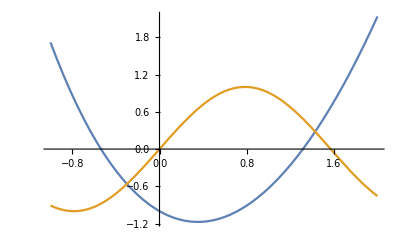

```mathematica
Plot[{x^2+E^-x-2, Sin[2x]}, {x, -1,2}]
```

```mathematica
FindRoot[x^2+E^-x-2==Sin[2x],{x,-1, 2}] (* Fix *)
FindRoot[x^2+E^-x-2==Sin[2x],{x,1, 2}]
```

{x→-0.29875}

{x→1.42861}

## 5.5

#### Вариант 10 | y’’[x]+y’[x] Tan[x]- Sin[x]==0, y(0)=-1, y’(0)=2 на отрезке x=>{0,9}

```mathematica
funcy=NDSolve[{y''[x]+y'[x]  Tan[x]- Sin[x]==0,y[0]==-1,y'[0]==2},y,{x,0,9}]
```

{{y→InterpolatingFunction[…]}}

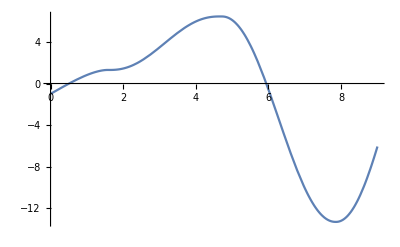

```mathematica
Plot[y[x]/.funcy,{x,0,9}]
```

#### 5.5.a | Найдите на заданном отрезке корни уравнения y(x)=0

```mathematica
r1=FindRoot[y[x]/.funcy,{x,5.9}]
```

{x→5.93897}

```mathematica
r2=FindRoot[y[x]/.funcy,{x,3.2}]
```

{x→0.511441}

#### 5.5.б | Найдите значения производной y’(x) в точках, где y(x)=0

```mathematica
D[y[x]/.funcy,x]/.r1
```

{-9.54781}

```mathematica
D[y[x]/.funcy,x]/.r2
```

{1.86348}

#### 5.5.в | Выберите одну из точек, в которых производная функции y(x)=0, и вычислите значение функции в этой точке

```mathematica
value=FindRoot[D[y[x]/.funcy,x]==0,{x,7.8}]
```

{x→7.85394}

```mathematica
y[x]/.funcy/.value
```

{-13.3329}

#### 5.5.г | С помощью функции FindMinimum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте ‘в’

```mathematica
FindMinimum[y[x]/.funcy,{x,8}]
```

{-13.3329,{x→7.85394}}

## 5.6

#### 5.6.а | Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях: y(x)=a+b*x+c*x^2+d*x^3+e*x^4 и y(x)=a+b*x+c*sin(x)+d*cos(x). Используя функцию Table, определите список численных данных, каждый элемент которого содержит два элемента (x,y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение Дy

#### 1)

```mathematica
dat1=Table[{x,(21+52x+73 x^2+17 x^3+33 x^4)(1+Random[Real, {-0.2,0.2}])}, {x,0,5,0.25}]
Length[dat1]
```

{{0.,17.6528},{0.25,44.7363},{0.5,74.6689},{0.75,129.811},{1.,185.035},{1.25,277.989},{1.5,442.2},{1.75,773.569},{2.,1125.},{2.25,1363.88},{2.5,2570.19},{2.75,3247.88},{3.,3507.79},{3.25,4791.89},{3.5,7440.2},{3.75,10071.9},{4.,12227.},{4.25,16017.6},{4.5,16279.},{4.75,18176.9},{5.,23861.7}}

21

#### 2)

```mathematica
dat2=Table[{x,(21+42x+84Sin[x]+35Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,55.2272},{0.25,83.6598},{0.5,103.486},{0.75,147.234},{1.,143.943},{1.25,150.657},{1.5,168.65},{1.75,165.329},{2.,150.548},{2.25,146.61},{2.5,154.356},{2.75,126.004},{3.,129.674},{3.25,110.661},{3.5,112.117},{3.75,98.2989},{4.,108.349},{4.25,118.481},{4.5,122.626},{4.75,149.719},{5.,159.763}}

#### 5.6.б | Изобразите полученные точки на координатной плоскости

```mathematica
1)
```

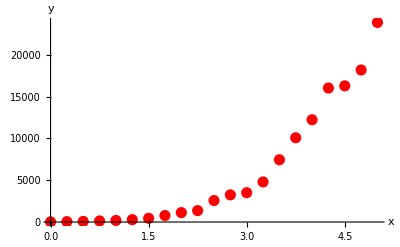

```mathematica
y1=ListPlot[dat1,PlotStyle->{PointSize[0.02],RGBColor[1,0,0]},AxesLabel->{"x","y"}]
```

```mathematica
2)
```

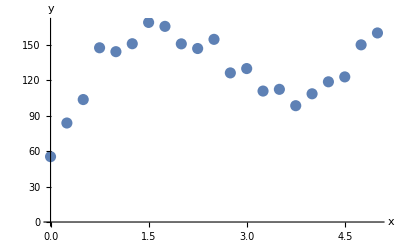

```mathematica
p1=ListPlot[dat2,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

#### 5.6.в | С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
1)
```

```mathematica
apr1=Fit[dat1,{1,x,x^2,x^3,x^4},x]
```

-170.663+1610.55 x-1936.95 x^2+822.022 x^3-62.8169 x^4

```mathematica
apr2=Fit[dat1,{1,x,Sin[x], Cos[x], Cos[2 x], Sin[2x]},x](*экспериментальные точки*)
```

-4794.94+4671.73 x+4803.75 Cos[x]-182.998 Cos[2 x]-2215.79 Sin[x]-488.297 Sin[2 x]

```mathematica
2)
```

```mathematica
aproc1=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

22.7315+41.0859 x+34.3599 Cos[x]+75.9522 Sin[x]

```mathematica
aproc2=Fit[dat2,{1,x,x^2,x^3, x^4, x^5},x](*экспериментальные точки*)
```

54.3543+127.197 x-20.0328 x^2-19.2341 x^3+6.20504 x^4-0.480177 x^5

#### 5.6.г | На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

```mathematica
1)
```

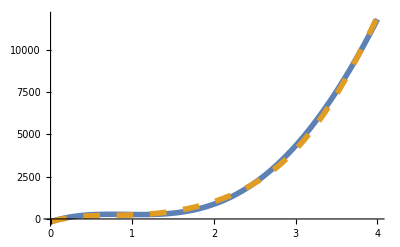

```mathematica
y2=Plot[{apr1,apr2},{x,0,4},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

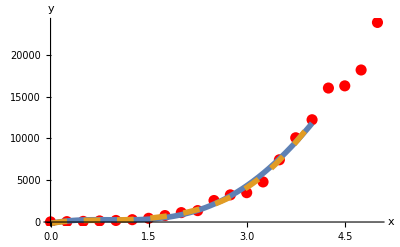

```mathematica
Show[y1,y2]
```

```mathematica
2)
```

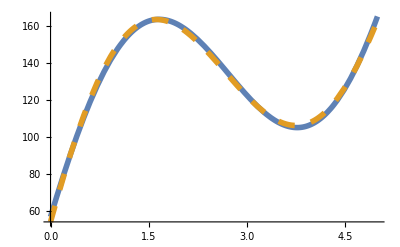

```mathematica
p2=Plot[{aproc1,aproc2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

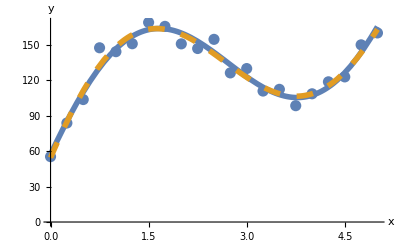

```mathematica
Show[p1,p2]
```